Risk Plots

## Unconstrained solutions

Plots that show the boundary of the feasible set, then draw in traces of solutions for iid mean process (typical of spike-and-slab Bayesian model).

Transfer file from server.  Parsing of parameter values, with special cases... 
	alpha = defines oracle		 		0 mins LS risk, and 1 mins risk, and other mins testimator risk
	beta = rate used by bidder if geometric		0 for universal (if omega=0, then bid = beta/n)
	omega = payout				0 indicates fixed bidding
	scale = scale parameter of universal distribution

### Functions for plotting and reading data ...

Idea is to make a file name based on parameter values.  Keep the name and parameter values as the first two items in a list with the data last.

```mathematica
Clear[fmt, getN, makeID, getData];

fmt[x_]:=With[{s= ToString[Round[100x]]},
If[StringLength[s]>1,s,StringJoin["0",s]]
]

makeID[α_,β_,ω_, scale_, n_] :=
{StringJoin["summary_risk_alpha",fmt[α],"_beta",fmt[β],"_omega",fmt[ω],"_scale",ToString[scale],"_n",ToString[n]],
{α,β,ω,scale,n}
}

getN[{_,_,_,_,n_}] :=n


getData[{name_,parms_},figureNumber_,server_]:=Module[
{f=ToString[figureNumber],
fullName,x},
fullName=StringJoin[" ~/C/bellman/figures/f",f,"1/",name];
If[StringLength[server]>1,
<<(StringJoin["!scp ",server,"C/bellman/figures/f",f,"/",name, fullName])];
x= Import[StringJoin["~/C/bellman/figures/f",f,"/",name], "Table"];
Print["found dimensions ", Dimensions[x]];
{name,parms,Sort[x,#1⟦3⟧<#2⟦3⟧&]} (* sort on angle *)
]
```

The function pickColumns adds 1 and flips sign to make work with log/log plot.

```mathematica
Clear[pickColumns, drawFeasibleSet,drawLogFeasibleSet];

pickColumns[simres_] := 1 -(#1⟦{7,8}⟧&)/@ simres

drawFeasibleSet[{name_,{α_,β_,ω_,σ_,n_},simres_},{join_:False,color_:Blue}]:=Module[
{xy =pickColumns[simres]},
ListPlot[xy,
Joined->join,
PlotRange->{{0,1.05Max[xy]},{0,1.05Max[xy]}},
AspectRatio->1,
PlotStyle->{color,PointSize[0.015]},
AxesLabel->{simres⟦1,1⟧,If[ω==0,
StringJoin["Bonferroni(",ToString[β],")"],
simres⟦1,2⟧]},
PlotLabel->StringJoin["Feasible Risks  (
StyleBox[\"n\",\nFontSlant->\"Italic\"]=",ToString[n],", ω=",ToString[ω],")"],
BaseStyle->{Gray,Larger,FontFamily->"Chalkboard",FontSize->10},
Epilog->{Orange,Line[{{0.0,0.0},{1000,1000}}] }
]
]

drawLogFeasibleSet[{name_,{α_,β_,ω_,σ_,n_},simres_},{join_:False,color_:Blue}] := Module[
{xy=pickColumns[simres]},
ListLogLogPlot[xy,
Print["2 log n =",2.Log[n]];
Joined->join,
PlotRange->{{1,1.2Max[xy]},{1,1.15Max[xy]}},
AspectRatio->1,
PlotStyle->{color,PointSize[0.015]},
AxesLabel->{simres⟦1,1⟧,If[ω==0,
StringJoin["Bonferroni(",ToString[β],")"],
simres⟦1,2⟧]},
PlotLabel->StringJoin["Feasible Risks  (
StyleBox[\"n\",\nFontSlant->\"Italic\"]=",ToString[n],", ω=",ToString[ω],")"],
BaseStyle->{Gray,Larger,FontFamily->"Chalkboard",FontSize->10}, 
Epilog->{ (* LogLogPlot exponentiates all before drawing, as if these are on log scale *)
Orange,Line[{{0.01,0.01},{100,100}}],
Red, Line[{{0,Log[1+2Log[n]]},{Log[20000],Log[20000+20000(2Log [n])]}}],
color,(*Arrow[Log[xy]]*)}]
]
```

```mathematica
Clear[drawFeasibleSets];

drawFeasibleSets[simres_List]:=Module[
{xy =pickColumns[#⟦3⟧]&/@simres,
colors=GrayLevel/@Range[0.2,0.9,0.7/Length[simres]],

ListPlot[xy,
PlotRange->{{0,1.05Max[xy]},{0,1.05Max[xy]}},
AspectRatio->1,
PlotStyle->{Blue,PointSize[0.015]},
AxesLabel->{simres⟦1,1⟧,If[ω==0,
StringJoin["Bonferroni(",ToString[β],")"],
simres⟦1,2⟧]},
PlotLabel->StringJoin["Feasible Risks  (
StyleBox[\"n\",\nFontSlant->\"Italic\"]=",ToString[n],", ω=",ToString[ω],")"],
BaseStyle->{Gray,Larger,FontFamily->"Chalkboard",FontSize->10},
Epilog->{Orange,Line[{{0.0,0.0},{1000,1000}}] }
]
]
```

```mathematica
?Range
```

Range[i_max] generates the list {1,2,…,i_max}. 
Range[i_min,i_max] generates the list {i_min,…,i_max}. 
Range[i_min,i_max,di] uses step di.

```mathematica
Range[1,2,{4}]
```

{{1}}

### Figure 1

The data that is produced has a list of 3 items
	file name
	parameter values (as alpha, beta, omega, scale and n)
	simulation results.

```mathematica
id = With[
{α=1,β=0.1,scale=2,n=500},
makeID[α,β,#,scale,n]&/@ {0.05,0.25,0.50,0.75}
]

getN[{_,_,_,_,n_}] :=n

f1Data=Table[getData[id⟦i⟧,""],{i,1,4}];
```

{{summary_risk_alpha100_beta10_omega05_scale2_n500,{1,0.1,0.05,2,500}},{summary_risk_alpha100_beta10_omega25_scale2_n500,{1,0.1,0.25,2,500}},{summary_risk_alpha100_beta10_omega50_scale2_n500,{1,0.1,0.5,2,500}},{summary_risk_alpha100_beta10_omega75_scale2_n500,{1,0.1,0.75,2,500}}}

Look for the angle where risk increases suddenly.

```mathematica
f1Data[[4,3]]//TableForm
```

Oracle(1) | Geom(0.1) | 0 | 0.75 | 500 | -14.2561 | 0 | -14.2561
Oracle(1) | Geom(0.1) | 15 | 0.75 | 500 | -13.7703 | 0 | -14.2561
Oracle(1) | Geom(0.1) | 30 | 0.75 | 500 | -12.3461 | 0 | -14.2561
Oracle(1) | Geom(0.1) | 45 | 0.75 | 500 | -10.0806 | 0 | -14.2561
Oracle(1) | Geom(0.1) | 60 | 0.75 | 500 | -7.12804 | 0 | -14.2561
Oracle(1) | Geom(0.1) | 65 | 0.75 | 500 | -6.02488 | 0 | -14.2561
Oracle(1) | Geom(0.1) | 70 | 0.75 | 500 | -4.87586 | 0 | -14.2561
Oracle(1) | Geom(0.1) | 75 | 0.75 | 500 | -3.68974 | 0 | -14.2561
Oracle(1) | Geom(0.1) | 80 | 0.75 | 500 | -2.47554 | 0 | -14.2561
Oracle(1) | Geom(0.1) | 85 | 0.75 | 500 | -1.2425 | 0 | -14.2561
Oracle(1) | Geom(0.1) | 90 | 0.75 | 500 | 7.27578×10^-11 | 0 | -14.2561
Oracle(1) | Geom(0.1) | 93 | 0.75 | 500 | 0.746105 | 0 | -14.2561
Oracle(1) | Geom(0.1) | 93.2 | 0.75 | 500 | 0.795795 | 0 | -14.2561
Oracle(1) | Geom(0.1) | 93.4 | 0.75 | 500 | 0.845476 | 0 | -14.2561
Oracle(1) | Geom(0.1) | 93.6 | 0.75 | 500 | 0.895146 | 0 | -14.2561
Oracle(1) | Geom(0.1) | 93.8 | 0.75 | 500 | 1.11844 | -6.51067 | -114.899
Oracle(1) | Geom(0.1) | 94 | 0.75 | 500 | 1.54896 | -7.50771 | -129.57
Oracle(1) | Geom(0.1) | 94.2 | 0.75 | 500 | 2.00095 | -8.01137 | -136.415
Oracle(1) | Geom(0.1) | 94.4 | 0.75 | 500 | 2.52174 | -8.82171 | -147.518
Oracle(1) | Geom(0.1) | 94.6 | 0.75 | 500 | 3.05103 | -9.41017 | -155.001
Oracle(1) | Geom(0.1) | 94.8 | 0.75 | 500 | 3.60552 | -9.98857 | -162.039
Oracle(1) | Geom(0.1) | 95 | 0.75 | 500 | 4.18441 | -10.5759 | -168.894
Oracle(1) | Geom(0.1) | 95.2 | 0.75 | 500 | 4.78701 | -11.1692 | -175.546
Oracle(1) | Geom(0.1) | 95.4 | 0.75 | 500 | 5.41299 | -11.7913 | -182.258
Oracle(1) | Geom(0.1) | 95.6 | 0.75 | 500 | 6.05748 | -12.4019 | -188.56
Oracle(1) | Geom(0.1) | 95.8 | 0.75 | 500 | 6.73224 | -13.0809 | -195.397
Oracle(1) | Geom(0.1) | 96 | 0.75 | 500 | 7.42909 | -13.7673 | -202.059
Oracle(1) | Geom(0.1) | 96.2 | 0.75 | 500 | 8.147 | -14.4564 | -208.509
Oracle(1) | Geom(0.1) | 96.4 | 0.75 | 500 | 8.88725 | -15.159 | -214.874
Oracle(1) | Geom(0.1) | 96.6 | 0.75 | 500 | 9.64977 | -15.8848 | -221.245
Oracle(1) | Geom(0.1) | 96.8 | 0.75 | 500 | 10.4344 | -16.6233 | -227.533
Oracle(1) | Geom(0.1) | 97 | 0.75 | 500 | 11.241 | -17.3779 | -233.77
Oracle(1) | Geom(0.1) | 98 | 0.75 | 500 | 15.5925 | -21.3772 | -264.143
Oracle(1) | Geom(0.1) | 99 | 0.75 | 500 | 20.477 | -25.7946 | -293.759
Oracle(1) | Geom(0.1) | 100 | 0.75 | 500 | 25.8599 | -30.5127 | -321.967
Oracle(1) | Geom(0.1) | 105 | 0.75 | 500 | 59.4929 | -56.9886 | -442.547
Oracle(1) | Geom(0.1) | 110 | 0.75 | 500 | 101.993 | -83.9437 | -528.84
Oracle(1) | Geom(0.1) | 115 | 0.75 | 500 | 151.564 | -112.4 | -599.673
Oracle(1) | Geom(0.1) | 120 | 0.75 | 500 | 204.568 | -132.7 | -638.977
Oracle(1) | Geom(0.1) | 125 | 0.75 | 500 | 259.94 | -154.439 | -673.753
Oracle(1) | Geom(0.1) | 135 | 0.75 | 500 | 371.803 | -185.429 | -711.237
Oracle(1) | Geom(0.1) | 150 | 0.75 | 500 | 529.466 | -224.89 | -741.217
Oracle(1) | Geom(0.1) | 165 | 0.75 | 500 | 662.877 | -263.512 | -756.869
Oracle(1) | Geom(0.1) | 180 | 0.75 | 500 | 760.805 | -295.071 | -760.805
Oracle(1) | Geom(0.1) | 195 | 0.75 | 500 | 813.327 | -317.9 | -756.839
Oracle(1) | Geom(0.1) | 210 | 0.75 | 500 | 817.601 | -342.284 | -746.467
Oracle(1) | Geom(0.1) | 225 | 0.75 | 500 | 775.515 | -389.247 | -707.497
Oracle(1) | Geom(0.1) | 240 | 0.75 | 500 | 707.958 | -471.804 | -598.729
Oracle(1) | Geom(0.1) | 255 | 0.75 | 500 | 623.224 | -500 | -541.929
Oracle(1) | Geom(0.1) | 270 | 0.75 | 500 | 500 | -500 | -500.035
Oracle(1) | Geom(0.1) | 285 | 0.75 | 500 | 353.552 | -500 | -500
Oracle(1) | Geom(0.1) | 300 | 0.75 | 500 | 183.013 | -500 | -500
Oracle(1) | Geom(0.1) | 315 | 0.75 | 500 | -1.26286×10^-8 | -500 | -500
Oracle(1) | Geom(0.1) | 330 | 0.75 | 500 | -12.3412 | -0.050739 | -14.2797
Oracle(1) | Geom(0.1) | 345 | 0.75 | 500 | -13.7702 | -0.00243124 | -14.2566
Oracle(1) | Geom(0.1) | 359 | 0.75 | 500 | -14.2539 | 0 | -14.2561

```mathematica
colors=GrayLevel /@ {0.2,0.4,0.6,0.8};
f1Plots=Table[drawFeasibleSet[f1Data⟦i⟧,colors⟦i⟧],{i,1,4}];
```

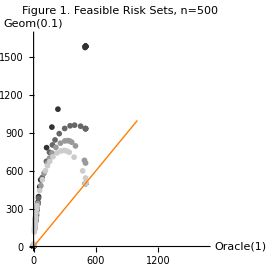

```mathematica
Show[f1Plots,PlotLabel->"Figure 1. Feasible Risk Sets, n=500"]
```

```mathematica
colors=GrayLevel /@ {0.2,0.4,0.6,0.8};
f1LogPlots=Table[drawLogFeasibleSet[f1Data⟦i⟧,colors⟦i⟧],{i,1,4}];
```

2 log n =12.4292

2 log n =12.4292

2 log n =12.4292

«1 more identical outputs»

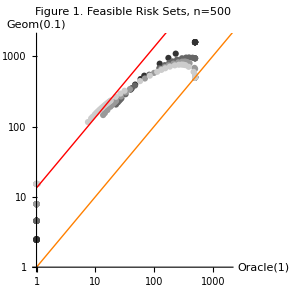

```mathematica
Show[f1LogPlots,PlotLabel->"Figure 1. Feasible Risk Sets, n=500"]
```

### Figure 2

```mathematica
id = With[
{α=0.1,β=0.1,scale=2,n=100},
makeID[α,β,#,scale,n]&/@ {0.05,0.25,0.50,0.75}
]

f2Data=Table[getData[id⟦i⟧,2,""],{i,1,4}];
```

{{summary_risk_alpha10_beta10_omega05_scale2_n100,{0.1,0.1,0.05,2,100}},{summary_risk_alpha10_beta10_omega25_scale2_n100,{0.1,0.1,0.25,2,100}},{summary_risk_alpha10_beta10_omega50_scale2_n100,{0.1,0.1,0.5,2,100}},{summary_risk_alpha10_beta10_omega75_scale2_n100,{0.1,0.1,0.75,2,100}}}

found dimensions {34,8}

found dimensions {34,8}

found dimensions {34,8}

«1 more identical outputs»

Look for the angle where risk increases suddenly.

```mathematica
f2Data[[1,3]]//TableForm
```

Oracle(0.1) | Geom(0.1) | 0 | 0.05 | 100 | -0.700083 | -43.9286 | -0.700083
Oracle(0.1) | Geom(0.1) | 15 | 0.05 | 100 | -12.0458 | -43.9286 | -0.700083
Oracle(0.1) | Geom(0.1) | 30 | 0.05 | 100 | -22.5706 | -43.9286 | -0.700083
Oracle(0.1) | Geom(0.1) | 45 | 0.05 | 100 | -31.5572 | -43.9286 | -0.700083
Oracle(0.1) | Geom(0.1) | 60 | 0.05 | 100 | -38.3933 | -43.9286 | -0.700083
Oracle(0.1) | Geom(0.1) | 65 | 0.05 | 100 | -40.1087 | -43.9286 | -0.700083
Oracle(0.1) | Geom(0.1) | 70 | 0.05 | 100 | -41.5189 | -43.9286 | -0.700083
Oracle(0.1) | Geom(0.1) | 75 | 0.05 | 100 | -42.6129 | -43.9286 | -0.700083
Oracle(0.1) | Geom(0.1) | 80 | 0.05 | 100 | -43.3828 | -43.9286 | -0.700083
Oracle(0.1) | Geom(0.1) | 85 | 0.05 | 100 | -43.8225 | -43.9286 | -0.700083
Oracle(0.1) | Geom(0.1) | 90 | 0.05 | 100 | -43.9286 | -43.9286 | -0.700083
Oracle(0.1) | Geom(0.1) | 95 | 0.05 | 100 | -43.4692 | -47.0498 | -39.0286
Oracle(0.1) | Geom(0.1) | 100 | 0.05 | 100 | -37.8152 | -51.4637 | -74.0958
Oracle(0.1) | Geom(0.1) | 105 | 0.05 | 100 | -29.1877 | -57.9316 | -103.431
Oracle(0.1) | Geom(0.1) | 110 | 0.05 | 100 | -17.6979 | -66.6742 | -131.441
Oracle(0.1) | Geom(0.1) | 115 | 0.05 | 100 | -2.9633 | -80.7094 | -166.07
Oracle(0.1) | Geom(0.1) | 120 | 0.05 | 100 | 14.6584 | -95.3707 | -194.504
Oracle(0.1) | Geom(0.1) | 125 | 0.05 | 100 | 35.9952 | -121.632 | -236.464
Oracle(0.1) | Geom(0.1) | 135 | 0.05 | 100 | 94.8235 | -192.83 | -326.931
Oracle(0.1) | Geom(0.1) | 150 | 0.05 | 100 | 186.868 | -193.587 | -327.544
Oracle(0.1) | Geom(0.1) | 165 | 0.05 | 100 | 266.333 | -193.921 | -327.689
Oracle(0.1) | Geom(0.1) | 180 | 0.05 | 100 | 327.718 | -194.13 | -327.718
Oracle(0.1) | Geom(0.1) | 195 | 0.05 | 100 | 366.817 | -194.288 | -327.698
Oracle(0.1) | Geom(0.1) | 210 | 0.05 | 100 | 380.959 | -194.43 | -327.639
Oracle(0.1) | Geom(0.1) | 225 | 0.05 | 100 | 369.181 | -194.573 | -327.528
Oracle(0.1) | Geom(0.1) | 240 | 0.05 | 100 | 332.302 | -194.739 | -327.306
Oracle(0.1) | Geom(0.1) | 255 | 0.05 | 100 | 272.882 | -194.958 | -326.743
Oracle(0.1) | Geom(0.1) | 270 | 0.05 | 100 | 195.224 | -195.224 | -323.67
Oracle(0.1) | Geom(0.1) | 285 | 0.05 | 100 | 110.455 | -179.639 | -243.659
Oracle(0.1) | Geom(0.1) | 300 | 0.05 | 100 | 55.2081 | -124.005 | -104.367
Oracle(0.1) | Geom(0.1) | 315 | 0.05 | 100 | 30.5703 | -45.0554 | -1.82237
Oracle(0.1) | Geom(0.1) | 330 | 0.05 | 100 | 21.358 | -43.9286 | -0.700083
Oracle(0.1) | Geom(0.1) | 345 | 0.05 | 100 | 10.6933 | -43.9286 | -0.700083
Oracle(0.1) | Geom(0.1) | 359 | 0.05 | 100 | 0.0666841 | -43.9286 | -0.700083

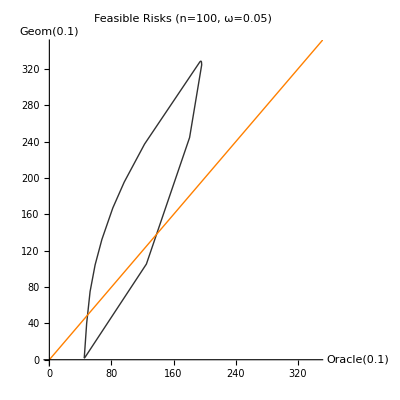
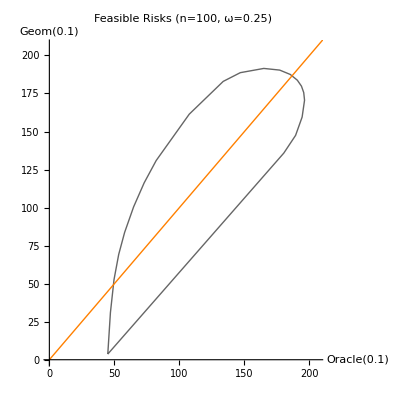
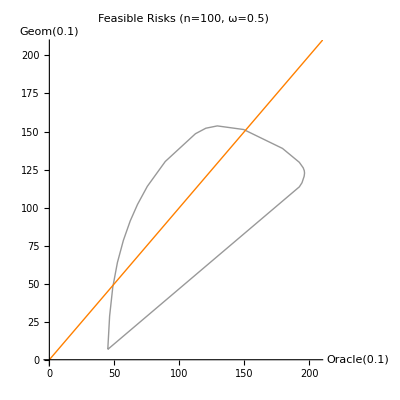
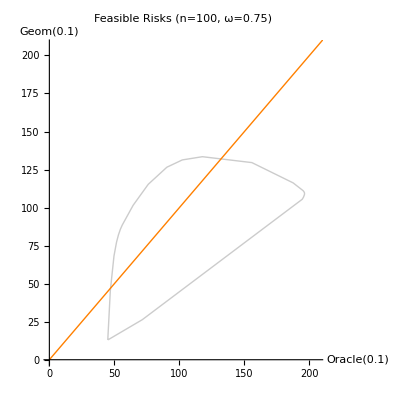

```mathematica
colors=GrayLevel /@ {0.2,0.4,0.6,0.8};
f2Plots=Table[drawFeasibleSet[f2Data⟦i⟧,{True,colors⟦i⟧}],{i,1,4}]
```

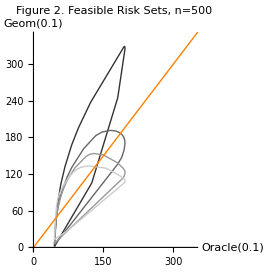

```mathematica
Show[f2Plots,PlotLabel->"Figure 2. Feasible Risk Sets, n=500"]
```

2 log n =9.21034

2 log n =9.21034

2 log n =9.21034

«1 more identical outputs»

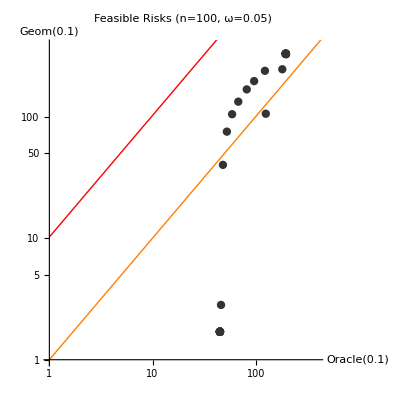
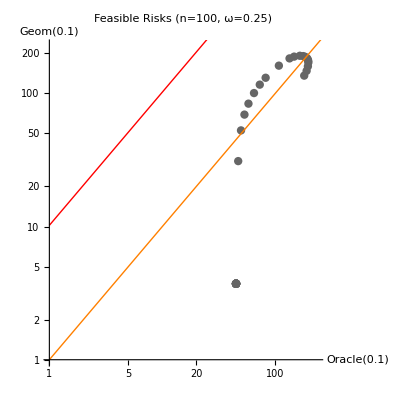
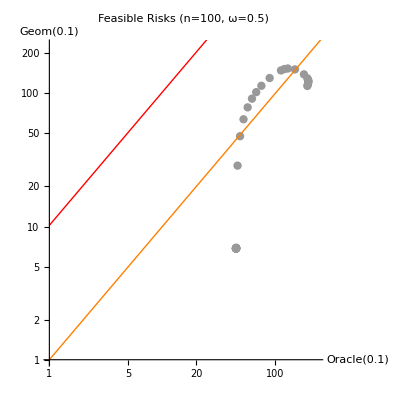
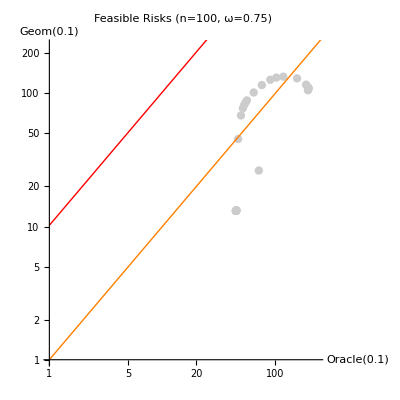

```mathematica
f2LogPlots=Table[drawLogFeasibleSet[f2Data⟦i⟧,{False,colors⟦i⟧}],{i,1,4}]
```

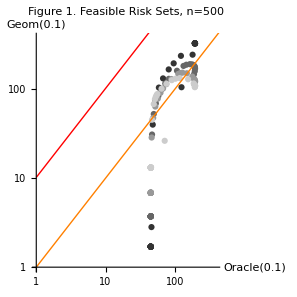

```mathematica
Show[f2LogPlots,PlotLabel->"Figure 1. Feasible Risk Sets, n=500"]
```

### Additional Plots

Log version for small risks; add one to everything to be logable.  Add 1 as in the F&G paper for the forced estimation of an intercept. Feasible set is not convex in this new coordinate system...

This plot shows the feasible set in a log-log plot to zoom in on the growth trajectory.  Probably should not have that diagonal arrow returning to the left since the set is not convex on the log-log scale.

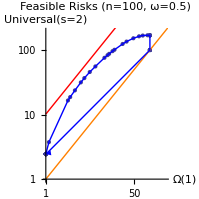
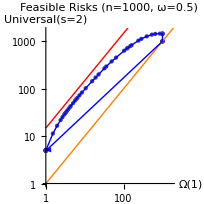
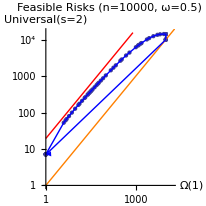
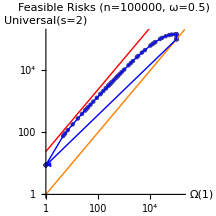

On the left is the testing oracle, on the right is the RI oracle.  Big difference...

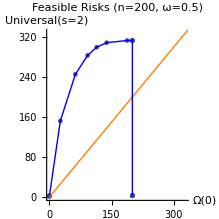
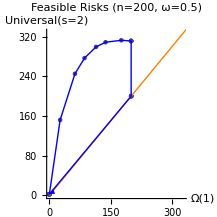

This is a plot to show the results for various values of n on the same graph. The align function rescales the oracle in the argument to match that in the reference set of coordinates.  Of course, all of the xy coordinate pairs (tables) need to be computed on the same grid.

```mathematica
(#⟦1⟧&/@xy[100])/(#⟦1⟧&/@xy[1000])xy[1000]
```

{{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1.,4.9781},{1.,7.46352},{1.,8.48179},{1.,9.09503},{1.,9.34627},{1.,9.54859},{1.,9.61351},{1.,9.6637},{1.,9.71541},{1.,9.76704},{1.,9.81115},{1.,9.83086},{1.,9.89444},{1.,9.92133},{1.,9.92079},{1.,9.91244},{1.,9.87986},{1.,9.81371},{1.14717,11.0705},{2.66802,24.7584},{2.94506,26.5979},{3.63303,31.9382},{4.72828,39.5592},{5.52181,45.2578},{7.02061,53.482},{9.00586,63.6606},{13.4679,82.3334},{15.4683,89.052},{16.5512,93.6673},{19.2555,102.521},{20.9676,108.264},{30.1292,129.591},{35.8269,140.711},{48.5095,156.406},{62.3546,161.448},{73.5121,160.915},{90.9595,152.964},{101.,145.346},{101,145.346},{101,145.346},{101,145.346},{101,145.346},{101,101.023},{101,101},{101,101},{101,101},{101,101},{101,101},{1.01568,4.95336},{1.00034,4.97694}}

```mathematica
Clear[ri];
ri[m_]:=With[
{ri=(#⟦2⟧/(2 Log[m] #⟦1⟧))& /@ (xy[m]),    (*  risk inflation as % of 2 log p *)
rpt=(#⟦1⟧/(2 Log[m]))& /@ (xy[m])                                               (* oracle risk per test *)
},
Sort[Transpose[{rpt,ri}],#1⟦1⟧≤#2⟦1⟧&]
]
```

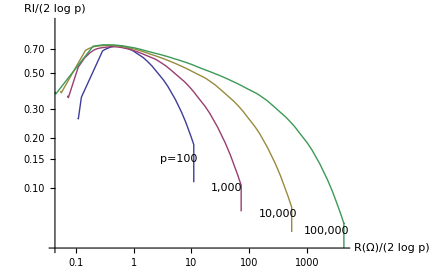

```mathematica
ListLogLogPlot[{ri[100],ri[1000],ri[10000],ri[100000]},
AxesLabel-> {"R(Ω)/(2 log p)","RI/(2 log p)"},
Epilog->{
Text["p=100",Log[{6,0.15}]],
Text["1,000",Log[{40,0.10}]],
Text["10,000",Log[{320,0.07}]],
Text["100,000",Log[{2150,0.055}]]},
Joined->True]
```

Now add the data for the 2 - point distribution with pZero signal.  Take off the leading pZero column, leaving oracle and bidder risks.

```mathematica
stripCol[x_]:= #⟦{2,3}⟧&/@x
Clear[rr];
With[{path=StringJoin["~/C/bellman/risk/omega",fmt[omega],"_scale",ToString[scale],"_n",ToString[n]]},
Print[path];
rr[0.5]=-stripCol[Import[StringJoin[path,"/m0.5"], "Table"]];
rr[1.0]=-stripCol[Import[StringJoin[path,"/m1.0"], "Table"]];
rr[1.5]=-stripCol[Import[StringJoin[path,"/m1.5"], "Table"]];
rr[2.0]=-stripCol[Import[StringJoin[path,"/m2.0"], "Table"]];
rr[2.5]=-stripCol[Import[StringJoin[path,"/m2.5"], "Table"]];
rr[3.0]=-stripCol[Import[StringJoin[path,"/m3.0"], "Table"]];
rr[3.5]=-stripCol[Import[StringJoin[path,"/m3.5"], "Table"]];
rr[4.0]=-stripCol[Import[StringJoin[path,"/m4.0"], "Table"]];
]
```

~/C/bellman/risk/omega50_scale2_n500

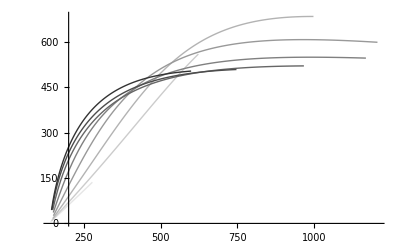

```mathematica
lp=ListPlot[{rr[0.5],rr[1.0],rr[1.5],rr[2.0],rr[2.5],rr[3.0],rr[3.5],rr[4.0]}, 
PlotRange->All,
Joined->True,
PlotStyle->GrayLevel/@Range[0.9,0.1,-0.1]]
```

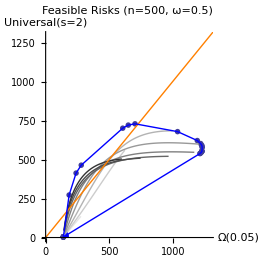

```mathematica
Show[cp,lp]
```

Two-sided risk, with improved scaled universal and || dual array code.

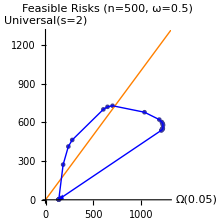
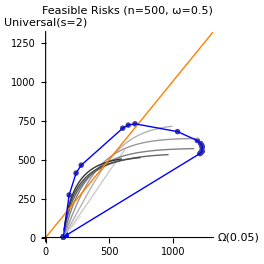

Two-sided risk, with improved scaled universal and |\ array code, adding risks for iid hypotheses.

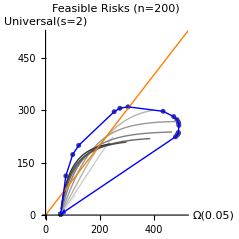
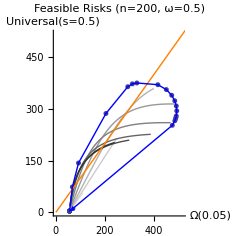
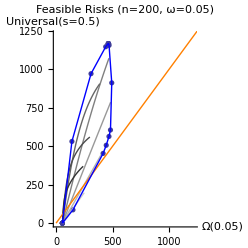

Two-sided risk